```mathematica
Table[-(0.001+i*0.0027)*x^2+(0.855+0.98*i)*x-(49.638+120*i),{i,0,3}]
```

{-49.638+0.855 x-0.001 x^2,-169.638+1.835 x-0.0037 x^2,-289.638+2.815 x-0.0064 x^2,-409.638+3.795 x-0.0091 x^2}

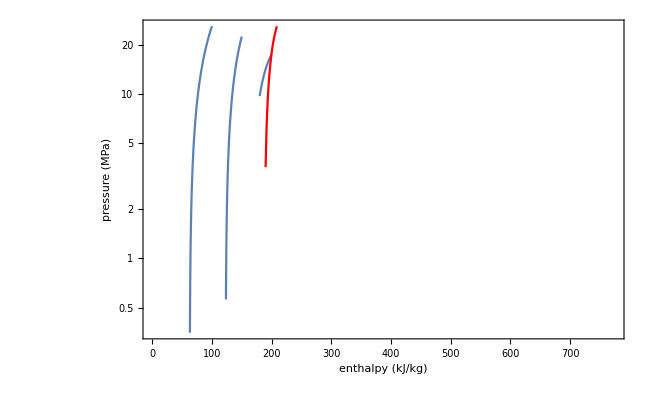

```mathematica
Module[{f1,g1,f2,g2,f3,h},

f1[x_]=-0.001*x^2+0.855*x-49.638;
(*g1[x_]=-0.0001531*x^2+0.1597*x-40.91;*)
(*f2[x_]=-0.0002*x^2+0.1599*x-40.979;*)
f2[x_]=-0.0037*x^2+1.8417*x-169.41;
(*g2[x_]=-0.00015*x^2+0.1596*x-41.475;*)

f3[x_]=-0.0268*x^2+11.864*x-1283.1;
(*f3[x_]=-0.0064*x^2+2.84*x-289;*)
(*f1list=Table[{x,f1[x]},{x,60,100}];
f2list=Table[{x,f2[x]},{x,530,560}];*)
h[x_]=-(0.001+i*0.0027)*x^2+(0.855+0.98*i)*x-(49.638+120*i);

Show[
(*LogPlot[f1[x],{x,60,100},PlotStyle->Blue],LogPlot[g1[x],{x,530,560},PlotStyle->Blue],
LogPlot[f2[x],{x,120,150},PlotStyle->Red],LogPlot[g2[x],{x,551,600},PlotStyle->Red],
LogPlot[f2[x-50],{x,120,250},PlotStyle->Green],*)

(*LogPlot[f1[x],{x,60,100},PlotStyle->Blue],
LogPlot[f2[x],{x,120,150},PlotStyle->Red],
LogPlot[f2[x-50],{x,120,200},PlotStyle->Green],*)
(*LogPlot[f1[x],{x,60,100},PlotStyle->Blue],
LogPlot[f1[x-50],{x,60,150},PlotStyle->Red],
LogPlot[f1[x-100],{x,60,200},PlotStyle->Green],*)
(*Table[LogPlot[f1[x-i*50],{x,60,100+i*50}],{i,0,3}],*)
(*LogPlot[f1[x],{x,60,100},PlotStyle->{Thick,Blue}],
LogPlot[-0.002*x^2+1.8*x-49.638,{x,120,150},PlotStyle->{Thick,Dashed,Red}],*)

Table[LogPlot[h[x],{x,60*(1+i),100+50*i}],{i,0,3}],
LogPlot[f3[x],{x,190,209},PlotStyle->Red],

Frame->True,FrameLabel->{Style["enthalpy (kJ/kg)",17],Style["pressure  (MPa)",17]},LabelStyle->{Black,14},
PlotRange->{{0,775},{Automatic,Automatic}(*{Log@0.5,Log@20}*)},Axes->False,ImageSize->650]
]
```

```mathematica
0.0037+0.0027
0.001+0.0027
```

0.0064

0.0037

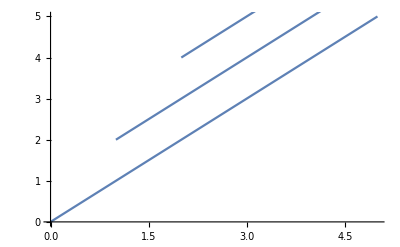

```mathematica
Show[Table[Plot[x+i,{x,i,i+5}],{i,0,3}]]
```

```mathematica
Module[{k},
k[x_]=x+j;
Show[Table[Plot[k[x],{x,j,j+5}],{j,0,3}]]
]
```

-Graphics-

```mathematica
Table[-(0.001+i*0.27)*x^2+(0.855+0.98*i)*x-(49.638+120*i),{i,0,3}]
```

{-49.638+0.855 x-0.001 x^2,-169.638+1.835 x-0.271 x^2,-289.638+2.815 x-0.541 x^2,-409.638+3.795 x-0.811 x^2}